| R | C | L
H(s) | (C R s)/(1+C R s+C L s^2) | 1/(1+C R s+C L s^2) | (C L s^2)/(1+C R s+C L s^2)
H(ω) | (ⅈ C R ω)/(1+ⅈ C R ω-C L ω^2) | 1/(1+ⅈ C R ω-C L ω^2) | -(C L ω^2)/(1+ⅈ C R ω-C L ω^2)

Filter Information For H(s)_R:

| 1 | 2
Poles | -0.5-0.866025 ⅈ | -0.5+0.866025 ⅈ
Zeroes | 0. | 
Center Freq | 1/(2 π) | 0

The Circuit Is A Bandpass Filter Centered At Angular Frequency 1

Bode Plot H(ω)_R:

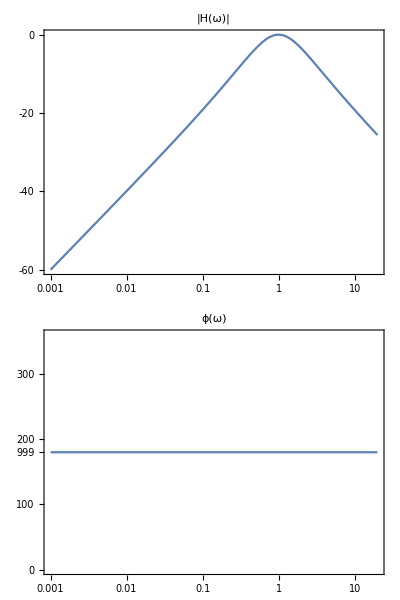

Filter Information For H(s)_C:

| 1 | 2
Poles | -0.5-0.866025 ⅈ | -0.5+0.866025 ⅈ
Zeroes | N/A | 
Center Freq | 1/(2 π) | 0

The Circuit Is Neither A Low-Pass, High-Pass Or BandPass Filter

Bode Plot H(ω)_C:

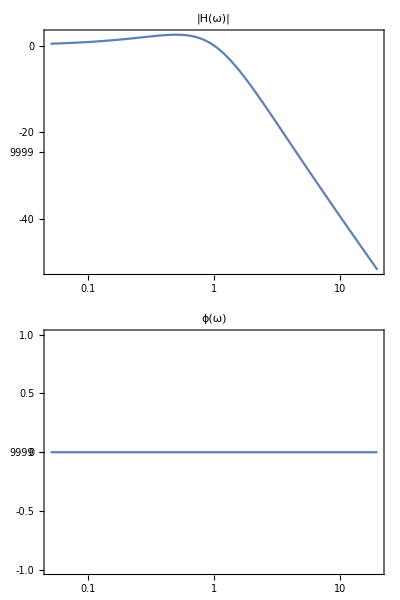

Filter Information For H(s)_L:

| 1 | 2
Poles | -0.5-0.866025 ⅈ | -0.5+0.866025 ⅈ
Zeroes | 0
0 | 
Center Freq | 1/(2 π) | 0

The Circuit Is Neither A Low-Pass, High-Pass Or BandPass Filter

Bode Plot H(ω)_L:

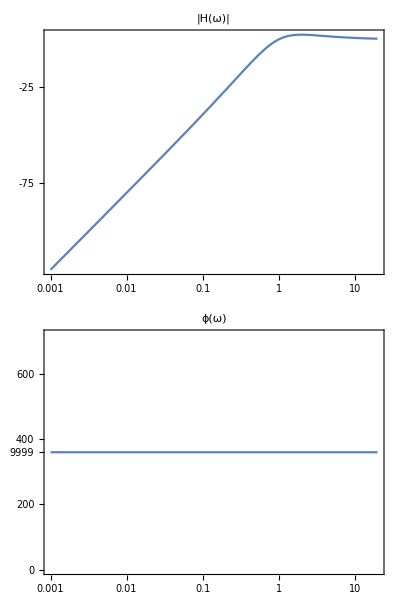

```mathematica
(*Transfer Functions for a simple RCL series circuit*)
(*There are three transfer functions for this circuit depending on which component Subscript[V, 0] is taken across*)

ZR = R;(*Input["Enter The Value Of Resistance:"]*)
ZC = 1/(s C);(*Input["Enter The Value Of Capacitance:"]*)
ZL=s L;(*Input["Enter The Value Of Inductance:"]*)

HS1 = Simplify[ZR/(ZR + ZC +ZL)]//ExpandAll;(*Resistor Voltage*)
HS2 = Simplify[ZC/(ZR + ZC+ ZL)]//ExpandAll;(*Cap Voltage*)
HS3 = Simplify[ZL/(ZR+ZC+ZL)]//ExpandAll;(*Inductor Voltage*)
Hω1 = HS1/.s->ⅉ ω;
Hω2=HS2/.s->ⅉ ω;
Hω3 = HS3 /.s->ⅉ ω;

testParameters={R->1,C->1,L->1};
TableForm[{{HS1,HS2,HS3},{Hω1,Hω2,Hω3}}, TableHeadings->{{"H(s)","H(ω)"},{"R","C","L"}},TableAlignments->{Center, Center}]

(*This Block Of Code Gives All Filter Info When Subscript[V, 0] Is Taken Across Resistor*)
StringTemplate["Filter Information For H(s)_R:"][]
eqn1=Denominator[HS1]==0;
eqn2 = Numerator[HS1]==0;
pole1 = s/.Solve[eqn1/.testParameters,s][[1]]//N;
pole2 = s/.Solve[eqn1/.testParameters,s][[2]]//N;
zero1 = s/.Solve[eqn2/.testParameters,s][[1]]//N;
zero2 = 0; 
(*zero2 = s/.Solve[eqn2/.testParameters,s][[2]]//N;*)
(*If filter has a second zero, uncomment this line and comment the previous line*)
wc=1/(√(L C))/.testParameters;
flag1=Limit[Abs[Hω1]/.testParameters,ω->0];
flag2 =Limit[Abs[Hω1]/.testParameters,ω->∞];
flag3 =Limit[Abs[Hω1]/.testParameters,ω->wc];
TableForm[{{pole1,pole2},{zero1},{wc/(2 π),0}},TableHeadings->{{"Poles","Zeroes","Center Freq"},{"1","2"}}]
If[flag1==1&&flag2==0 &&flag3 ==0,output=StringForm["The Circuit Is a Low-Pass Filter Centered At Angular Frequency ``",wc], If[flag2 ==1 && flag1 == 0 && flag3 ==0, output=StringForm["The Circuit Is A High-Pass Circuit Centered At Angular Frequency ``", wc], output=StringForm["The Circuit Is A Bandpass Filter Centered At Angular Frequency `` ", wc]]];
Style[output,Purple,16]
StringTemplate["Bode Plot H(ω)_R:"][]
BodePlot[Hω1/.testParameters,PlotLabel->{"|H(ω)|","ϕ(ω)"}]

(*The Block Of Code Gives All Filter Info When Subscript[V, 0] Is Taken Across Capacitor*)

StringTemplate["Filter Information For H(s)_C:"][]
eqn3=Denominator[HS2]==0;
eqn4 = Numerator[HS2]==0;
pole3 = s/.Solve[eqn3/.testParameters,s][[1]]//N;
pole4 = s/.Solve[eqn3/.testParameters,s][[2]]//N;
(*zero1 = s/.Solve[eqn2/.testParameters,s][[1]]//N;*)
(*zero2 = 0; *)
(*zero2 = s/.Solve[eqn2/.testParameters,s][[2]]//N;*)
(*If filter has a second zero, uncomment this line and comment the previous line*)
wk=1/(√(L C))/.testParameters;
flag4=Limit[Abs[Hω2]/.testParameters,ω->0];
flag5 =Limit[Abs[Hω2]/.testParameters,ω->∞];
flag6 =Limit[Abs[Hω2]/.testParameters,ω->wk];
TableForm[{{pole3,pole4},{"N/A"},{wk/(2 π),0}},TableHeadings->{{"Poles","Zeroes","Center Freq"},{"1","2"}}]
If[flag4==1 &&flag5==0 &&flag6 ==0,output=StringForm["The Circuit Is a Low-Pass Filter Centered At Angular Frequency ``",wk], If[flag5 ==1 && flag4 == 0 && flag6 ==0, output=StringForm["The Circuit Is A High-Pass Filter Centered At Angular Frequency ``", wk],
If[flag6==1 && flag4 ==0 && flag5 == 0, output= StringForm["The Circuit Is A BandPass Filter Centered At Angular Frequency ``", wk], 
output=StringForm["The Circuit Is Neither A Low-Pass, High-Pass Or BandPass Filter" ]]]];
Style[output,Purple,16]
StringTemplate["Bode Plot H(ω)_C:"][]
BodePlot[Hω2/.testParameters,PlotLabel->{"|H(ω)|","ϕ(ω)"}]

(*This Block Of Code Gives All Filter Info When Subscript[V, 0] Is Taken Across Inductor*)

StringTemplate["Filter Information For H(s)_L:"][]
eqn5=Denominator[HS3]==0;
eqn6= Numerator[HS3]==0;
pole5 = s/.Solve[eqn5/.testParameters,s][[1]]//N;
pole6 = s/.Solve[eqn5/.testParameters,s][[2]]//N;
(*zero1 = s/.Solve[eqn2/.testParameters,s][[1]]//N;*)
(*zero2 = 0; *)
(*zero2 = s/.Solve[eqn2/.testParameters,s][[2]]//N;*)
(*If filter has a second zero, uncomment this line and comment the previous line*)
zeroL=s/.Solve[eqn6,s];
wk2=1/(√(L C))/.testParameters;
flag7=Limit[Abs[Hω3]/.testParameters,ω->0];
flag8 =Limit[Abs[Hω3]/.testParameters,ω->∞];
flag9 =Limit[Abs[Hω3]/.testParameters,ω->wk2];
TableForm[{{pole5,pole6},{zeroL},{wk/(2 π),0}},TableHeadings->{{"Poles","Zeroes","Center Freq"},{"1","2"}}]
If[flag7==1 &&flag8==0 &&flag9 ==0,output=StringForm["The Circuit Is a Low-Pass Filter Centered At Angular Frequency ``",wk2], If[flag8 ==1 && flag7 == 0 && flag9 ==0, output=StringForm["The Circuit Is A High-Pass Filter Centered At Angular Frequency ``", wk2],
If[flag9==1 && flag7 ==0 && flag8 == 0, output= StringForm["The Circuit Is A BandPass Filter Centered At Angular Frequency ``", wk2], 
output=StringForm["The Circuit Is Neither A Low-Pass, High-Pass Or BandPass Filter" ]]]];
Style[output,Purple,16]
StringTemplate["Bode Plot H(ω)_L:"][]
BodePlot[Hω3/.testParameters,PlotLabel->{"|H(ω)|","ϕ(ω)"}]
```